```mathematica
(* Use Mathematica to compute the derivatives of the fit functions wrt each parameter *)
(* R. Sheehan 19 - 10 - 2021 *)
Clear[η, Id, Is, k, T]
Vd = η k T Log[1+(Id/Is)];
D[Vd,Id]
D[Vd,η]
D[Vd, T]
D[Vd, Is]
```

(k T η)/((1+Id/Is) Is)

k T Log[1+Id/Is]

k η Log[1+Id/Is]

-(Id k T η)/((1+Id/Is) Is^2)

0.727721

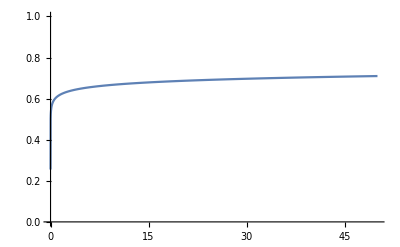

```mathematica
η=1; (* Ideality *)
T = 273.15+25; (* Temperature in K *)
k=8.61733×10^-5; (* Physical constants in J / C K *)
Is = 5000×10^-14; (* Saturation Current in mA *)
Vd/.Id->100
Plot[Vd,{Id,-0, 50},PlotRange->{{0,50},{-0,1}}]
```